(2 √(2/π))/(4+p^2)

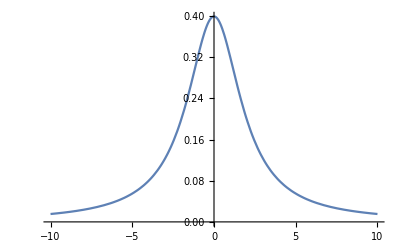

4/(4+p^2)

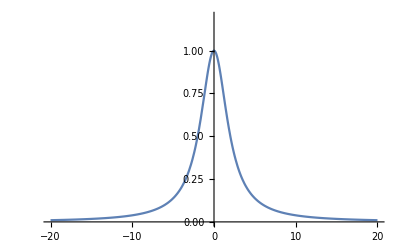

20/(25+ω^2)

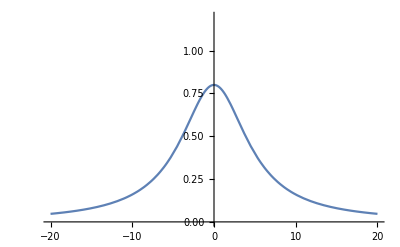

```mathematica
FourierTransform[Exp[-2 Abs[x]],x,p]
Plot[%,{p,-10,10}]
FullSimplify[Integrate[Exp[-2 Abs[x]] Exp[-I p x],{x,-Infinity,Infinity},Assumptions->{{x,p}∈Reals}],Assumptions->{{x,p}∈Reals}]
Plot[%,{p,-20,20},PlotRange->{0,1.2}]
FullSimplify[Integrate[2 Exp[-5 Abs[t]]Exp[-I ω t],{t,-Infinity,Infinity},Assumptions->{{t,ω}∈Reals}],Assumptions->{{t,ω}∈Reals}]
Plot[%,{ω,-20,20},PlotRange->{0,1.2}]
```

0.25 ⅇ^(-0.005 p^2)

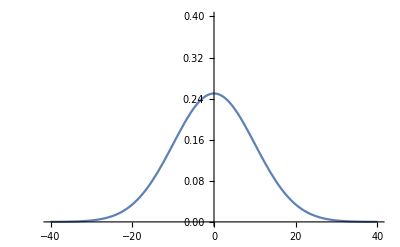

```mathematica
Clear[x,p];
FullSimplify[Integrate[1/(4 √(2 π 0.01)) Exp[-x^2/(2 0.01)] Exp[-I p x],{x,-Infinity,Infinity},Assumptions->{{x,p}∈Reals}],Assumptions->{{x,p}∈Reals}]
Plot[%,{p,-40,40},PlotRange->{0,0.4}]
```